Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zee=(GetYodaRaw[NotebookDirectory[]<>"Zee.yoda"]);
```

3 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta_inc/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

3 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta_inc/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

This contains Hist1D objects:

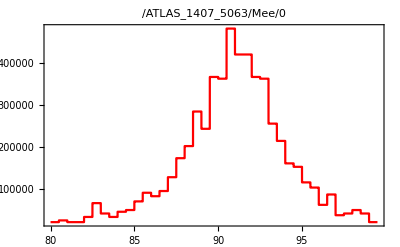

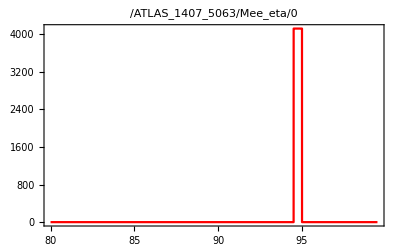

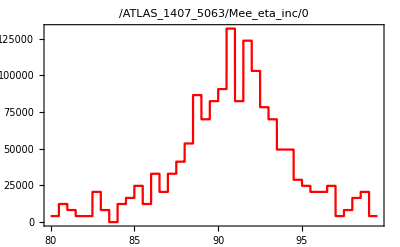

```mathematica
Hee=HistogramPlot[Zee[[1]],PlotStyle->{Red}]
HeeEta=HistogramPlot[Zee[[2]],PlotStyle->{Red}]
HeeEtaInc=HistogramPlot[Zee[[3]],PlotStyle->{Red}]
```